```mathematica
data = Import["C:\\Users\\Leoleo\\Desktop\\TCC\\Mathematica\\Fitting\\116.dat"];
```

```mathematica
Raio = Table[data[[i,1]],{i,15}];
```

```mathematica
Errococo:=Table[0,{i,15}]
```

```mathematica
Vtotal = Table [data[[i,3]],{i,15}];
```

```mathematica
Erro = Table[data[[i,5]],{i,15}];
```

```mathematica
RCTotal = Table[{{Raio[[i]],Vtotal[[i]]},ErrorBar[Erro[[i]]]},{i,15}];
```

```mathematica
RCtot:=Table[{Raio[[i]],Vtotal[[i]]},{i,15}]
```

```mathematica
Vgas = Table[data[[i,4]],{i,15}];
```

```mathematica
RCgas = Table[{Raio[[i]],Vgas[[i]]},{i,15}];
```

```mathematica
RCTG = Table [{RCTotal[[i]],RCgas[[i]]},{i,15}];
```

```mathematica
coco:=Table[{Raio[[i]],Vgas[[i]],Vtotalerro[[i]]},{i,15}]
```

```mathematica
coco//TableForm
```

0.295522 | -0.234178 | 20.94
Global`ErrorBar[3.4]
0.985821 | -1.95065 | 39.95
Global`ErrorBar[3.29]
1.62537 | -1.68024 | 51.54
Global`ErrorBar[2.96]
2.18881 | 5.43454 | 67.92
Global`ErrorBar[3.45]
3.17687 | 13.5993 | 80.22
Global`ErrorBar[2.93]
3.76791 | 18.0705 | 83.33
Global`ErrorBar[3.08]
4.35896 | 21.8567 | 91.38
Global`ErrorBar[2.83]
4.8903 | 24.2219 | 101.65
Global`ErrorBar[5.4]
6.19403 | 27.7912 | 104.77
Global`ErrorBar[4.21]
7.16418 | 29.5757 | 108.62
Global`ErrorBar[2.1]
8.0597 | 30.9882 | 108.48
Global`ErrorBar[2.1]
8.95522 | 33.3072 | 108.73
Global`ErrorBar[2.1]
9.85075 | 36.6602 | 110.24
Global`ErrorBar[2.1]
10.7463 | 38.4926 | 110.63
Global`ErrorBar[2.33]
11.6418 | 36.585 | 111.52
Global`ErrorBar[4.74]

```mathematica
TableForm[data,TableHeadings->{None,{"Raio","","Vtotal","Vgás","Erro"}}]
```

Raio |  | Vtotal | Vgás | Erro
0.295522 | 7.58904 | 20.94 | -0.234178 | 3.4
0.985821 | 7.79329 | 39.95 | -1.95065 | 3.29
1.62537 | 8.47973 | 51.54 | -1.68024 | 2.96
2.18881 | 9.15955 | 67.92 | 5.43454 | 3.45
3.17687 | 9.76846 | 80.22 | 13.5993 | 2.93
3.76791 | 9.48569 | 83.33 | 18.0705 | 3.08
4.35896 | 8.74732 | 91.38 | 21.8567 | 2.83
4.8903 | 7.95629 | 101.65 | 24.2219 | 5.4
6.19403 | 6.20847 | 104.77 | 27.7912 | 4.21
7.16418 | 5.25717 | 108.62 | 29.5757 | 2.1
8.0597 | 4.68539 | 108.48 | 30.9882 | 2.1
8.95522 | 4.27244 | 108.73 | 33.3072 | 2.1
9.85075 | 3.43065 | 110.24 | 36.6602 | 2.1
10.7463 | 1.87414 | 110.63 | 38.4926 | 2.33
11.6418 | 0.66706 | 111.52 | 36.585 | 4.74

```mathematica
{{"Raio", "", "Vtotal", "Vgás", "Erro"}, {0.295522, 7.58904, 20.94, -0.234178, 3.4}, {0.985821, 7.79329, 39.95, -1.95065, 3.29}, {1.62537, 8.47973, 51.54, -1.68024, 2.96}, {2.18881, 9.15955, 67.92, 5.43454, 3.45}, {3.17687, 9.76846, 80.22, 13.5993, 2.93}, {3.76791, 9.48569, 83.33, 18.0705, 3.08}, {4.35896, 8.74732, 91.38, 21.8567, 2.83}, {4.8903, 7.95629, 101.65, 24.2219, 5.4}, {6.19403, 6.20847, 104.77, 27.7912, 4.21}, {7.16418, 5.25717, 108.62, 29.5757, 2.1}, {8.0597, 4.68539, 108.48, 30.9882, 2.1}, {8.95522, 4.27244, 108.73, 33.3072, 2.1}, {9.85075, 3.43065, 110.24, 36.6602, 2.1}, {10.7463, 1.87414, 110.63, 38.4926, 2.33}, {11.6418, 0.66706, 111.52, 36.585, 4.74}}
```

{{0.295522,7.58904,20.94,-0.234178,3.4},{0.985821,7.79329,39.95,-1.95065,3.29},{1.62537,8.47973,51.54,-1.68024,2.96},{2.18881,9.15955,67.92,5.43454,3.45},{3.17687,9.76846,80.22,13.5993,2.93},{3.76791,9.48569,83.33,18.0705,3.08},{4.35896,8.74732,91.38,21.8567,2.83},{4.8903,7.95629,101.65,24.2219,5.4},{6.19403,6.20847,104.77,27.7912,4.21},{7.16418,5.25717,108.62,29.5757,2.1},{8.0597,4.68539,108.48,30.9882,2.1},{8.95522,4.27244,108.73,33.3072,2.1},{9.85075,3.43065,110.24,36.6602,2.1},{10.7463,1.87414,110.63,38.4926,2.33},{11.6418,0.66706,111.52,36.585,4.74}}

```mathematica
Needs["ErrorBarPlots`"]
```

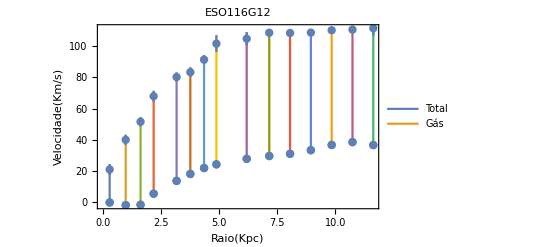

```mathematica
ErrorListPlot[RCTG,Mesh->All,Joined->True ,Frame->True,PlotLabel->"ESO116G12",FrameLabel->{"Raio(Kpc)","Velocidade(Km/s)"},PlotLegends->{"Total","Gás"}]
```

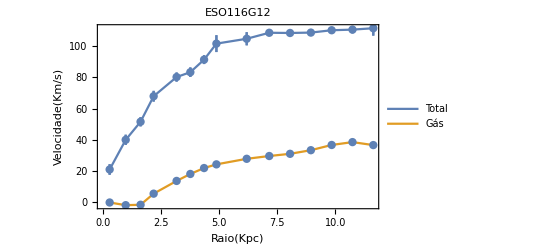

```mathematica
ErrorListPlot[{Table[{RCtot[[i]],ErrorBar[Erro[[i]]]},{i,15}],Table[{RCgas[[i]],ErrorBar[0]},{i,15}]},Mesh->All,Joined->True ,Frame->True,PlotLabel->"ESO116G12",FrameLabel->{"Raio(Kpc)","Velocidade(Km/s)"},PlotLegends->{"Total","Gás"}]
```